# Final Project Hongyi Gu, Haoyan Deng

## (1) Read in all the images from the training set (recall the same was done in HW6). Using the best parameters from the segmentation algorithms (recall HW9A), specify a new set of features for the textures that are based on your segmentation. For example, the number of segments found, the average size of the segments, the most common orientation of the segments, number of neighbors of each segment, etc. (all these, and more, can be extracted directly from the segmented image using ComponentMeasurements). You may also want to use DeleteSmallComponents as a kind of de-noising. Explain (a) how you do the segmentation and (b) what each of your features is and how it is extracted/calculated.

```mathematica
(*Reading all the training images and test images.*)
```

```mathematica
training=FileNames["*.jpg",NotebookDirectory[]<>"texturesTraining/"];
alltraining=Import[#]&/@training;
testing=FileNames["*.jpg",NotebookDirectory[]<>"texturesTest/"];
alltesting=Import[#]&/@testing;

(*Now we perform image segmentation calculation to all training set images. We used watershedComponents function with the method option 'MinimumSaliency'. We choose to use option 0.45 because this would give relatively reliable features (lines, areeas, orientations etc.)for most images by observation. We also used DeleteSmallComponents as a denoising method to get rid of very small components that have area less than 50.*)
textureimg=DeleteSmallComponents[WatershedComponents[alltraining[[#]],Method->{"MinimumSaliency",.45},CornerNeighbors->True],50]&/@Range[1,195];

(* 
We write this following function to generate a relatively reliable calcution of the deviation of orientations of all components of an image
. The orientation of each component is represented as angle in radian. Since the mathematica built in function for standard deviation calculation for a set of angle values does not take the wrapped nature of angles into account (for example, if a angle is -pi/2+0.001 radian and another angle is 3*pi/2-0.001, the standard deviation calculation in mathematica would be large while in fact the two angles represent almost the same orientations of two components), we take such nature into account in this following function by limiting all difference of angles to with in range 0 - pi/2, aand calculate the average difference of all component pairs.
*)
angleStandardDev[orientation_]:=Module[{},size=Dimensions[orientation];
sum=0;
temp=0;
For[i=1,i≤size[[1]],i++,For[j=i+1,j≤size[[1]],j++,temp=Abs[orientation[[i]]-orientation[[j]]];
If[temp≥(3/2)*Pi,sum+=2*Pi-temp];
If[temp<(3/2)*Pi&&temp≥Pi,sum+=temp-Pi];
If[temp≥(1/2)*Pi&&temp<Pi,sum+=Pi-temp];
If[temp<(1/2)*Pi,sum+=temp]];];
sum/(size[[1]]*(size[[1]]-1))*2]
```

```mathematica
(*The following are the features we calculated from our image segmentations of all training images. We also give a list plot for each feature to represent the value distribution of a certain feature over the 195 training images. Ideally, if we can see some clear separation and 'clusters' on a feature plot (for example, for a specific feature, most class1 images would give small values and most class2 images would give large values), then we can say this feature is 'resonable' in that it gives information that would be helpful for classifer to train and later classify test sets.*)
```

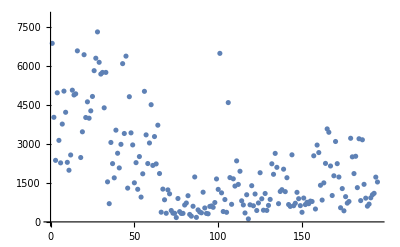

```mathematica
(*This feature is the standard deviation of the area of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Area and take standardDeviation for all the 195 training image.*)
stdArea= StandardDeviation[ComponentMeasurements[textureimg[[#]],"Area"][[;;,2]]]&/@Range[1,195];
ListPlot[stdArea]
```

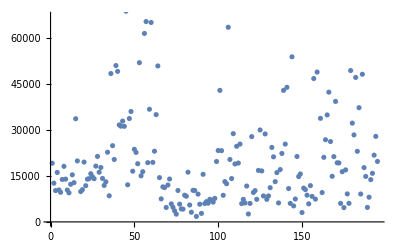

```mathematica
(*This feature is the max value of the areas of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Area and take Max for all the 195 training image.*)
maxArea=Max[ComponentMeasurements[textureimg[[#]],"Area"][[;;,2]]]&/@Range[1,195];
ListPlot[maxArea]
```

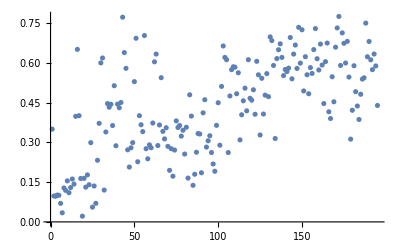

```mathematica
(*This feature is the deviation value of the orientations of the segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Orientation and call our own angleStandardDev function for all the 195 training image.*)
anglestd =angleStandardDev[ComponentMeasurements[textureimg[[#]],"Orientation"][[;;,2]]]&/@Range[1,195];
ListPlot[anglestd]
```

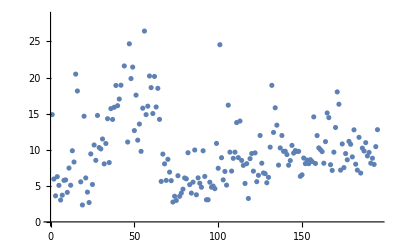

```mathematica
(*This feature is the standard deviation of the widths of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Width and take standardDeviation for all the 195 training image.*)
widthofComponents=StandardDeviation[ComponentMeasurements[textureimg[[#]],"Width"][[;;,2]]]&/@Range[1,195];
ListPlot[widthofComponents]
```

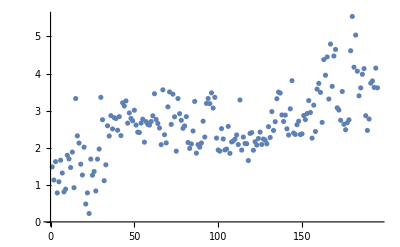

```mathematica
(*This feature is the standard deviation of the neighbor counts of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as NeighborCount and take standardDeviation for all the 195 training image.*)
neighborofComponents=StandardDeviation[ComponentMeasurements[textureimg[[#]],"NeighborCount"][[;;,2]]]&/@Range[1,195];
ListPlot[neighborofComponents]
```

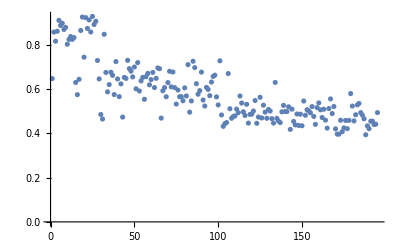

```mathematica
(*This feature is the mean of elogation of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Elongation and take the mean value for all the 195 training image.*)
meanElo=Mean[ComponentMeasurements[textureimg[[#]],"Elongation"][[;;,2]]]&/@Range[1,195];
ListPlot[meanElo]
```

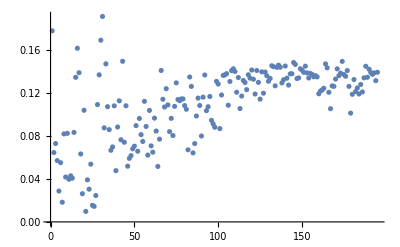

```mathematica
(*This feature is the standard deviation of eccentricity of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Eccentricity and take the StandardDeviation value for all the 195 training image.*)
stdeccentricity=StandardDeviation[ComponentMeasurements[textureimg[[#]],"Eccentricity"][[;;,2]]]&/@Range[1,195];
ListPlot[stdeccentricity]
```

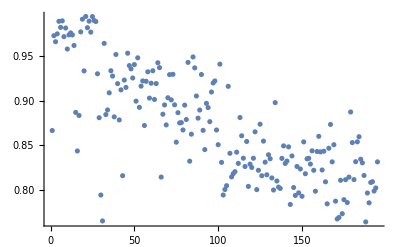

```mathematica
(*This feature is the mean value of eccentricity of segmentations of an image. It is calculated by calling ComponentMeasurements, specifying option as Eccentricity and take the mean value for all the 195 training image.*)
meaneccentricity=Mean[ComponentMeasurements[textureimg[[#]],"Eccentricity"][[;;,2]]]&/@Range[1,195];
ListPlot[meaneccentricity]
```

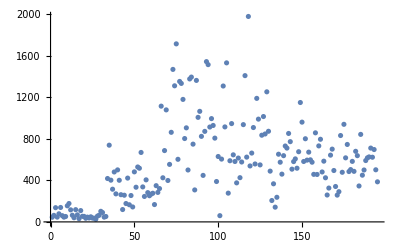

```mathematica
(*This feature is the number of segmentation of an image. It is calculated by calling ComponentMeasurements, specifying option as Count and take the Length for all the 195 training image.*)
count = Length[ComponentMeasurements[textureimg[[#]],"Count"][[;;,2]]]&/@Range[1,195];
ListPlot[count]
```

## (2) Combine these new features into a feature vector and (try to) classify the elements in the test set correctly.From HW6, you may recall that commands such as Nearest, FindClusters, and Classify may come in handy for this.I recommend Classify[{example1 -> class1, example2 -> class2, ...}] where the examples are your feature vectors and the classes are the class #s.The Classifier should be built using all the images from the training set.Using this classifier, how many of textures from the test set are correctly classified?Show your test routine. class #1: 1-36 fabric class #2: 37-72 fur class #3: 73-108 wood grain (coarse) class #4: 109-144 wood grain (fine) class #5: 145-180 birch bark class #6: 181-216 oak bark

```mathematica
(*construct all the above 9 features of the training set images as a feature matrix. Each image should has a feature vector of length 9.*)
features1 = Transpose[{stdArea, maxArea, anglestd, widthofComponents, neighborofComponents,meanElo, stdeccentricity, meaneccentricity,count }];
```

```mathematica
(*Create the labeling of the classes for all the training images*)
Kernel = ConstantArray[0, {195}];
Kernel[[1;;33]] = 1;
Kernel[[34;;65]] = 2;
Kernel[[66;;98]] = 3;
Kernel[[99;;130]] = 4;
Kernel[[131;;162]] = 5;
Kernel[[163;;195]] = 6;
```

```mathematica
(*relate the feature vector of image to its corresponding class.*)
traininginput1 = Thread[features1->Kernel];
```

```mathematica
(*Use function Classify to generation a classifier function using all the feature vectors constructed. We have tried many options for this classify function. The option LogisticRegression returns the best classification result for the test sets.*)
classifier1 = Classify[traininginput1,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(*Create the labeling of the classes for all the test images*)
testtruth= ConstantArray[0, {21}];
testtruth[[1;;3]] = 1;
testtruth[[4;;7]] = 2;
testtruth[[8;;10]] = 3;
testtruth[[11;;14]] = 4;
testtruth[[15;;18]] = 5;
testtruth[[19;;21]] = 6;
```

```mathematica
(*Now we perform image segmentation calculation to all test set images using the same methods as the training set.*)
testimg=DeleteSmallComponents[WatershedComponents[alltesting[[#]],Method->{"MinimumSaliency",.45},CornerNeighbors->True],50]&/@Range[1,21];
```

```mathematica
(*calculate the nine features for the testing set images using exactly the same approaches as what was done to the training set.*)
teststdArea= StandardDeviation[ComponentMeasurements[testimg[[#]],"Area"][[;;,2]]]&/@Range[1,21];
testmaxArea=Max[ComponentMeasurements[testimg[[#]],"Area"][[;;,2]]]&/@Range[1,21];
testanglestd =angleStandardDev[ComponentMeasurements[testimg[[#]],"Orientation"][[;;,2]]]&/@Range[1,21];
testwidthofComponents=StandardDeviation[ComponentMeasurements[testimg[[#]],"Width"][[;;,2]]]&/@Range[1,21];
testneighborofComponents=StandardDeviation[ComponentMeasurements[testimg[[#]],"NeighborCount"][[;;,2]]]&/@Range[1,21];
testmeanElo=Mean[ComponentMeasurements[testimg[[#]],"Elongation"][[;;,2]]]&/@Range[1,21];
teststdeccentricity=StandardDeviation[ComponentMeasurements[testimg[[#]],"Eccentricity"][[;;,2]]]&/@Range[1,21];
testmeaneccentricity=Mean[ComponentMeasurements[testimg[[#]],"Eccentricity"][[;;,2]]]&/@Range[1,21];
testcount = Length[ComponentMeasurements[testimg[[#]],"Count"][[;;,2]]]&/@Range[1,21];
```

```mathematica
(*construct all the above 9 features of the test set images as a feature matrix. Each image should has a feature vector of length 9.*)
testfeatures1 = Transpose[{teststdArea, testmaxArea, testanglestd, testwidthofComponents, testneighborofComponents,testmeanElo, teststdeccentricity, testmeaneccentricity,testcount }];
```

```mathematica
(*input the calculated feature matrix of the test images to the Classifer, the output is the classification result*)
classifier1result = classifier1 [testfeatures1]
```

{1,1,1,2,2,2,2,3,3,3,4,4,4,4,5,6,5,5,6,6,6}

```mathematica
(*20 images in the test set are correctly classified. There is only one misclassification.*)
classifier1result-testtruth
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}

## (3) Compare your segmentation - based features with your earlier statistically - based features from HW6. Which does better? Now combine all the features together, and see if you can get improved classification. State clearly how you are going to train and test your classifier.

```mathematica
(*The result using classify function and segment based features work better than the result using statistically based features in HW6. Note that in HW6 we did not use the classify function.*)


(*Now we try to classify based on statistical features in HW6 and apply the classify function. In HW6, we used 4 features as shown below. We are going to use these 4 features only for training the classifier. The result has 4 misclassifications -- generally good but not as good as our previous classification in question 2.*)
```

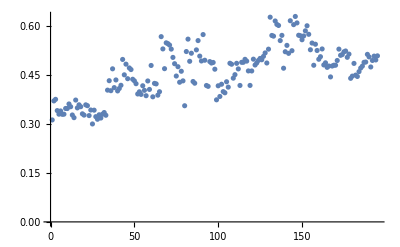

```mathematica
(*This feature is the mean value of the image data of a specific image.*)
mean =  Mean[Flatten[ImageData[#]]]&/@alltraining;
ListPlot[mean]
```

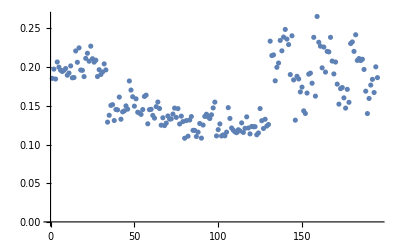

```mathematica
(*This feature is the standard deviation of the image data of a specific image.*)
std = ImageMeasurements[#,"StandardDeviation"]&/@alltraining;
ListPlot[std ]
```

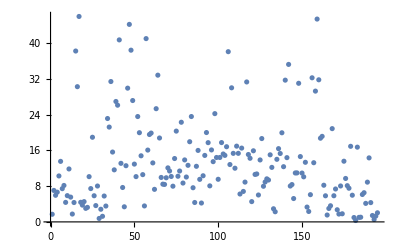

```mathematica
(*This feature is the magnitude of the second component of each image's fft.*)
FFT = Fourier[Flatten[ImageData[#]]]&/@alltraining;
FFTcol2 = Abs[FFT[[All,2]]];
ListPlot[FFTcol2]
```

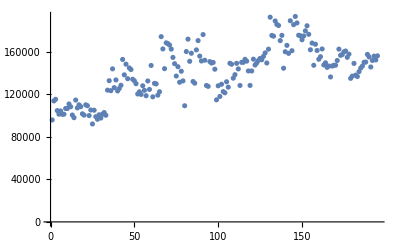

```mathematica
(*This feature is the sum of pixels after a low pass filtering of each image*)
imagelowpassed = LowpassFilter[#,0.4]&/@alltraining;
lowpassedData = Flatten[ImageData[#]]&/@imagelowpassed;
sumOfLowPass = Total[#]&/@lowpassedData;
ListPlot[sumOfLowPass ]
```

```mathematica
(*construct all the above 4 features of the training set images as a feature matrix. Each image should has a feature vector of length 4.*)
features2 = Transpose[{mean,std,FFTcol2,sumOfLowPass}];

(*relate the feature vector of image to its corresponding class.*)
traininginput2 = Thread[features2->Kernel];
```

```mathematica
(*Use function Classify to generation a classifier function using all the feature vectors constructed.*)
classifier2= Classify[traininginput2,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(*calculate the four features for the testing set images using exactly the same approaches as what was done to the training set.*)
testmean =  Mean[Flatten[ImageData[#]]]&/@alltesting;
teststd = ImageMeasurements[#,"StandardDeviation"]&/@alltesting;
testFFT = Fourier[Flatten[ImageData[#]]]&/@alltesting;
testFFTcol2 = Abs[testFFT[[All,2]]];
testimagelowpassed = LowpassFilter[#,0.4]&/@alltesting;
testlowpassedData = Flatten[ImageData[#]]&/@testimagelowpassed;
testsumOfLowPass = Total[#]&/@testlowpassedData;
```

```mathematica
(*construct all the above 4 features of the test set images as a feature matrix. Each image should has a feature vector of length 4.*)
testfeatures2 = Transpose[{testmean,teststd,testFFTcol2,testsumOfLowPass}];
```

```mathematica
(*input the calculated feature matrix of the test images to the Classifer, the output is the classification result*)
classifier2result = classifier2[testfeatures2]
```

{1,1,1,2,2,2,3,6,4,3,4,4,4,4,5,5,5,5,3,6,6}

```mathematica
(*17 images in the test set are correctly classified. There are 4 misclassifications. So this result gets worse.*)
classifier2result-testtruth
```

{0,0,0,0,0,0,1,3,1,0,0,0,0,0,0,0,0,0,-3,0,0}

```mathematica
(*Now we try to combombine all features together and apply the classify function. Using the 13 features, we get 0 misclassifications -- it is the best classification result we get so far. Details are shown below:*)
```

```mathematica
(*construct all the above 13 features of the training set images as a feature matrix. Each image should has a feature vector of length 13.*)
features3 = Transpose[{stdArea, maxArea, anglestd, widthofComponents, neighborofComponents,meanElo, stdeccentricity, meaneccentricity,count ,mean,std,FFTcol2,sumOfLowPass}];

(*relate the feature vector of image to its corresponding class.*)
traininginput3= Thread[features3->Kernel];
```

```mathematica
(*Use function Classify to generation a classifier function using all the feature vectors constructed.*)
classifier3= Classify[traininginput3,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(*construct all the above 13 features of the test set images as a feature matrix. Each image should has a feature vector of length 13.*)
testfeatures3 = Transpose[{teststdArea, testmaxArea, testanglestd, testwidthofComponents, testneighborofComponents,testmeanElo, teststdeccentricity, testmeaneccentricity,testcount,testmean,teststd,testFFTcol2,testsumOfLowPass}];
```

```mathematica
(*input the calculated feature matrix of the test images to the Classifer, the output is the classification result*)
classifier3result = classifier3[testfeatures3]
```

{1,1,1,2,2,2,2,3,3,3,4,4,4,4,5,5,5,5,6,6,6}

```mathematica
(*All the 21 images in the test set are correctly classified. The classification has 100% correctness.*)
classifier3result-testtruth
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## (4) Using your newly acquired expertise in image processing, can you think of any new features that might help?Propose at least one new feature, and create a test to see if it does (or does not) improve the classification accuracy).(Perhaps use Radon or ImageLines, Fourier or Wavelet coefficients, or some kind of nonlinear filter?) Make sure you explain what the new feature is, and how you test to see if it helps improve things.

```mathematica
(*We came up with a new feature: the number of lines of an image returned by the function ImageLines*)
```

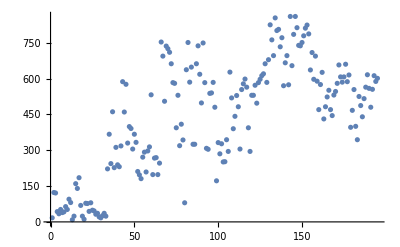

```mathematica
(*calculate the number of lines of an image using function ImageLines for all training set images.*)
lines = Dimensions[ImageLines[#, 1/3]][[1]]&/@alltraining;
ListPlot[lines]
```

```mathematica
(*construct all the above 14 features of the training set images as a feature matrix. Each image should has a feature vector of length 14.*)
features4 = Transpose[{stdArea, maxArea, anglestd, widthofComponents, neighborofComponents,meanElo, stdeccentricity, meaneccentricity,count ,mean,std,FFTcol2,sumOfLowPass, lines}];

(*relate the feature vector of image to its corresponding class.*)
traininginput4= Thread[features4->Kernel];
```

```mathematica
(*Use function Classify to generation a classifier function using all the feature vectors constructed.*)
classifier4= Classify[traininginput4,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(*calculate this new feature for the testing set images using exactly the same approach as what was done to the training set.*)
testlines = Dimensions[ImageLines[#, 1/3]][[1]]&/@alltesting;
```

```mathematica
(*construct all the above 14 features of the test set images as a feature matrix. Each image should has a feature vector of length 14.*)
testfeatures4= Transpose[{teststdArea, testmaxArea, testanglestd, testwidthofComponents, testneighborofComponents,testmeanElo, teststdeccentricity, testmeaneccentricity,testcount,testmean,teststd,testFFTcol2,testsumOfLowPass,testlines}];
```

```mathematica
(*input the calculated feature matrix of the test images to the Classifer, the output is the classification result*)
classifier4result = classifier4[testfeatures4]
```

{1,1,1,2,2,2,2,3,3,3,4,4,4,4,5,5,5,5,6,6,6}

```mathematica
(*All the 21 images in the test set are correctly classified. The classification has 100% correctness. Since our classifer in question 3 have already reached 100% of correctness for the test cases, this classifier is not able to show any improvements. However, we think this classifier (classifier4) would be a little bit better than previous classifier3 because the newly added feature, the number of lines of an image,is actually very good (as what is shown on the feature plot of 'lines', the feature values of images from the same class are 'clustered' together). Therefore, we think the newly added feature will theoretically contribute to a more accurate classification for the Classifier function.*)
classifier4result-testtruth
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}